#### Task Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Once[Get["Project2.m","IX1501"]];
?randomExample
```

randomExample[n] gives n randomnumbers from a secret distribution.

#### Setting up the random data

```mathematica
n=10000;
𝕩=randomNumber[1, n];
Short[𝕩];
𝕩sort=Sort[𝕩];
Δ=1/n;
𝕡data=Δ/2+Range[0,1-Δ,Δ]//N;
𝕩𝕡data=Transpose[{𝕩sort,𝕡data}];
```

#### FindDistribution

```mathematica
distOne=randomNumber[1, n];
distTwo=randomNumber[2, n];
distThree=randomNumber[3, n];
distFour=randomNumber[4, n];
distFive=randomNumber[5, n];
distSix=randomNumber[6, n];
```

FindDistribution[distOne] (* Exponential *)
FindDistribution[distTwo] (* Geometric *)
FindDistribution[distThree] (* Gamma *)
FindDistribution[distFour] (* Normal *) 
FindDistribution[distFive (* Binomial *)
FindDistribution[distSix] (* Poisson *)

#### Illustrating the data

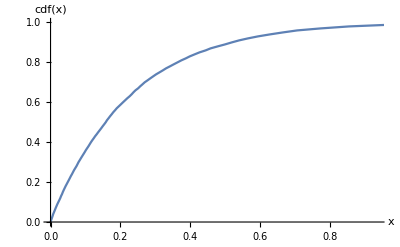

```mathematica
ListPlot[𝕩𝕡data,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}];
qdata=Table[{Quantile[𝕩,q],q},{q,0,1,0.01}];
ListLinePlot[qdata,AxesLabel->{HoldForm[x],HoldForm[cdf[x]]}]
```

#### Straight Line approach declaration

```mathematica
x=Mean[𝕩];
s=StandardDeviation[𝕩];
𝒩=NormalDistribution[x,s];
𝕡model=CDF[𝒩,𝕩sort];
comparedata=Transpose[{𝕡model,𝕡data}];
```

#### Illustrating Straight Line approach ND matched with Data

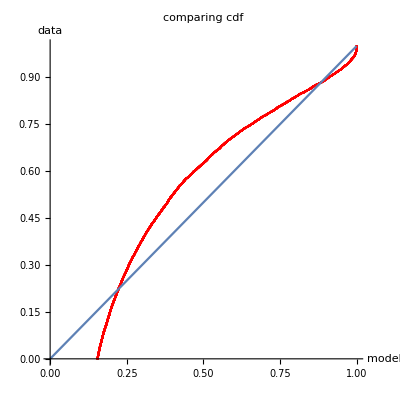

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing cdf",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```

#### Straight Line Approach - randomNumber[1] and Gamma

```mathematica
Clear[α,β];
𝒢=EstimatedDistribution[𝕩,GammaDistribution[α,β]];
𝕡model=CDF[𝒢,𝕩sort];
comparedata=Transpose[{𝕡model,𝕡data}];
```

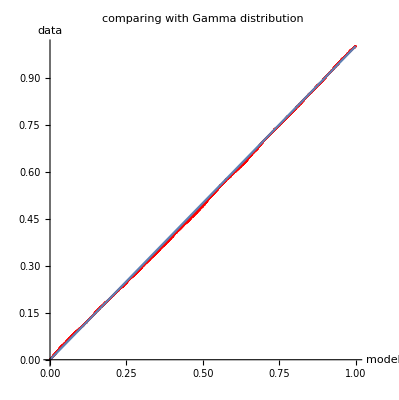

```mathematica
dataplot=ListPlot[comparedata,PlotStyle->Red,AxesLabel->{"model","data"},PlotLabel->"comparing with Gamma distribution",AspectRatio->Automatic];
lineplot=Plot[x,{x,0,1}];
Show[dataplot,lineplot]
```